```mathematica
(*Using Zhu, Xiong paper*)
(* Distance between nuclei*)

(**)

(* L equation and coefficients *)
σ[r_]:=r/p-1/2;
α[n_]:=(n+1)(n+1/2);
β[n_,r_]:=2 n^2+(4p-2σ[r])n-A +p^2-2p σ[r]-σ[r]/2;
γ[n_,r_]:=(n-1)(n-2σ[r]-1/2)+σ[r](σ[r]-1/2);

(* Create a continued fraction equation for the coefficients of L equation *)

lCoeff2[n_,r_]:=β[0,r]/α[0]+Simplify[ContinuedFractionK[-α[i-1]γ[i,r],β[i,r],{i,1,n}]] ;

(* M equation and coefficients *)

w=-A +p^2/2;      q= -p^2/4;
v[n_]:=(w-n^2)/q;
(* Evaluate as a continued fraction *)
mCoeffV0[n_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,n}]];

mCoeffV1[n_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,n}]];

(* Parameters:
n: Depth of the continued fraction,
 R: Internuclear distance,
 gerade: flag indicating whether we are calculating gerade or ungerade states
output:
R , electron energy, total energy, separation constant, and p value 
*)
energySingleR[n_,R_, gerade_]:=
Module[{asAndps,pe,energy,aa},
(*Now find p and A *)
If[gerade==1, 
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV0[n]==0},{A,p},Reals],
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV1[n]==0},{A,p},Reals]];
aa=Sort[asAndps[[All,1,2]], Greater][[1]];
pe=Sort[asAndps[[All,2,2]], Greater][[1]];
energy = (-2)/R^2 pe^2;
{R,energy, energy + 1/R,aa,pe}
]
```

```mathematica
allRs = Table[0.2+i*0.1,{i,0,9}];
allRs = Join[allRs, Table[1+.5*i,{i,1,8}]];
allRs = Join[allRs, Table[5+i,{i,1,5}]];

energiesGerade = Map[energySingleR[3,#1,1] &, allRs];
energiesUngerade = Map[energySingleR[3,#1,2] &, allRs];
```

```mathematica
Prepend[energiesGerade, {"R", "E", "E+1/r", "A", "p"}]  //MatrixForm
Prepend[energiesUngerade, {"R", "E","E+1/r", "A", "p"}]  //MatrixForm
```

(R | E | E+1/r | A | p
0.2 | -6.50361 | -1.50361 | 19.2757 | 0.360655
0.3 | -5.81983 | -2.48649 | 175.774 | 0.511754
0.4 | -5.27552 | -2.77552 | 198.466 | 0.649647
0.5 | -4.83822 | -2.83822 | 218.834 | 0.777674
0.6 | -4.48148 | -2.81482 | 30.6031 | 0.898146
0.7 | -4.18616 | -2.75759 | 255.124 | 1.01272
0.8 | -3.93852 | -2.68852 | 271.721 | 1.12264
0.9 | -3.72861 | -2.6175 | 287.554 | 1.22886
1. | -3.54905 | -2.54905 | 302.754 | 1.33211
1.1 | -3.39429 | -2.4852 | 317.417 | 1.43302
1.5 | -2.95083 | -2.28416 | 371.99 | 1.822
2. | -2.63638 | -2.13638 | 433.864 | 2.29625
2.5 | -2.4621 | -2.0621 | 491.12 | 2.77382
3. | -2.36086 | -2.02752 | 545.139 | 3.25943
3.5 | -2.29797 | -2.01225 | 596.728 | 3.75167
4. | -2.25565 | -2.00565 | 646.407 | 4.24796
4.5 | -2.22496 | -2.00274 | 694.536 | 4.74634
5. | -2.20134 | -2.00134 | 741.373 | 5.24564
6 | -2.16637 | -1.9997 | 16608. | 6.24457
7 | -2.14043 | -1.99757 | 919.107 | 7.24158
8 | -2.11874 | -1.99374 | 1003.68 | 8.23405
9 | -2.09856 | -1.98745 | 1086.12 | 9.21909
10 | -2.07822 | -1.97822 | 1166.79 | 10.1937)

(R | E | E+1/r | A | p
0.2 | -0.841481 | 4.15852 | 33.4451 | 0.129729
0.3 | -0.911818 | 2.42152 | 39.6245 | 0.202563
0.4 | -1.03317 | 1.46683 | 44.6816 | 0.287495
0.5 | -1.20111 | 0.798885 | 49.0907 | 0.387478
0.6 | -1.39266 | 0.274004 | 53.0632 | 0.500679
0.7 | -1.58212 | -0.153551 | 56.7159 | 0.622591
0.8 | -1.75267 | -0.502667 | 395.73 | 0.748901
0.9 | -1.89725 | -0.786142 | 417.783 | 0.876577
1. | -2.01521 | -1.01521 | 66.3746 | 1.0038
1.1 | -2.10899 | -1.1999 | 459.254 | 1.12957
1.5 | -2.31161 | -1.64494 | 534.677 | 1.61262
2. | -2.36744 | -1.86744 | 619.719 | 2.17598
2.5 | -2.35029 | -1.95029 | 698.046 | 2.7101
3. | -2.31526 | -1.98193 | 111.724 | 3.2278
3.5 | -2.2797 | -1.99399 | 841.77 | 3.73673
4. | -2.24845 | -1.99845 | 909.103 | 4.24118
4.5 | -2.22222 | -2. | 974.188 | 4.74341
5. | -2.20044 | -2.00044 | 1037.4 | 5.24457
6 | -2.16704 | -2.00038 | 1159.29 | 6.24554
7 | -2.14278 | -1.99992 | 1276.36 | 7.24556
8 | -2.12404 | -1.99904 | 1389.63 | 8.24435
9 | -2.10851 | -1.9974 | 1499.83 | 9.24093
10 | -2.09461 | -1.99461 | 1607.45 | 10.2338)

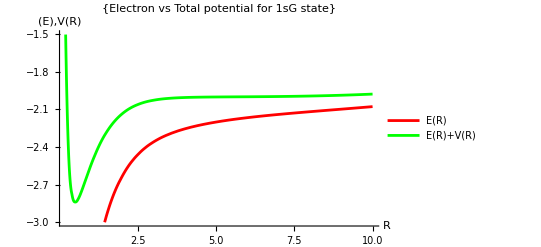

```mathematica
eG = Interpolation[Transpose[{energiesGerade[[All,1]],energiesGerade[[All,2]]}]];
eGTotal = Interpolation[Transpose[{energiesGerade[[All,1]],energiesGerade[[All,3]]}]];
Plot[{eG[x],eGTotal[x]},{x,0.2,10}, PlotStyle->{Red,Green},PlotRange->{1,-3}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 1sG (Gerade) state"}, PlotLegends->{"E(R)","E(R)+V(R)"}]
```

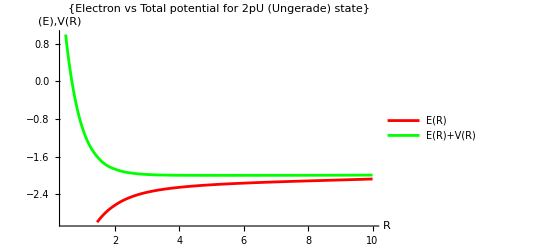

```mathematica
eU = Interpolation[Transpose[{energiesUngerade[[All,1]],energiesGerade[[All,2]]}]];
eUTotal = Interpolation[Transpose[{energiesUngerade[[All,1]],energiesUngerade[[All,3]]}]];
Plot[{eU[x],eUTotal[x]},{x,0.2,10}, PlotStyle->{Red,Green},PlotRange->{1,-3}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 2pU (Ungerade) state"}, PlotLegends->{"E(R)","E(R)+V(R)"}]
```

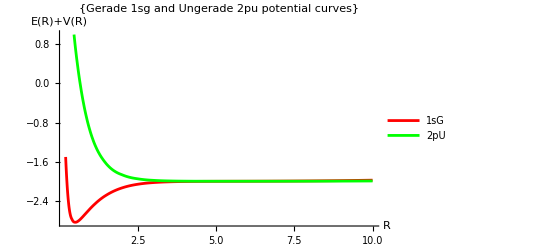

```mathematica
Plot[{eGTotal[x],eUTotal[x]},{x,0.2,10}, PlotStyle->{Red,Green},PlotRange->{1,-3}, AxesLabel->{"R", "E(R)+V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Gerade 1sg and Ungerade 2pu total potential curves"}, PlotLegends->{"1sG","2pU"}]
```

```mathematica
uG
```